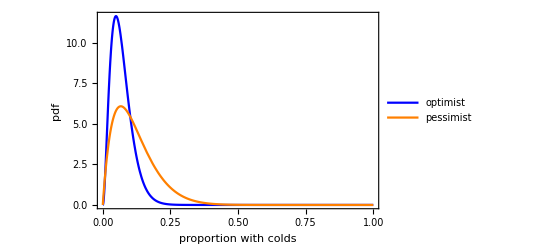

```mathematica
Plot[{PDF[BetaDistribution[3,40],x],PDF[BetaDistribution[2,15],x]},{x,0,1},PlotRange->Full,PlotStyle->{Blue,Orange},FrameLabel->{"proportion with colds","pdf"},Frame->{True,True,False,False},BaseStyle->{FontSize->14},PlotLegends->Placed[{"optimist","pessimist"},Center]]
```

```mathematica
realData= RandomVariate[BinomialDistribution[100,0.15],{10}];
```

```mathematica
pOptimistGivenData =NIntegrate[PDF[BetaDistribution[3,40],p]*Likelihood[BinomialDistribution[100,p],realData],{p,0,1}]
pPessimistGivenData =NIntegrate[PDF[BetaDistribution[2,15],p]*Likelihood[BinomialDistribution[100,p],realData],{p,0,1}]
```

1.11949×10^-13

2.72436×10^-13